# Cálculo de las secciones transversales de absorción, esparcimiento y extinción

```mathematica
ConfigureMaTeX[
"pdfLaTeX"->"C:\\Users\\Poh\\AppData\\Local\\Programs\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.03.1\\bin\\gswin64c.exe"
]
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\Users\Poh\AppData\Local\Programs\MiKTeX\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10.03.1\bin\gswin64c.exe}

```mathematica
Needs["MaTeX`"]
```

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
vlight=3*^17 ;(*nm s^-1*)
ϵ0=8.854187812*10^(-3)(*F/nm*);
```

Definiendo los factores de depolarización considerando los casos para un elipsoide oblato (a=b) L1= L2 y uno prolato (b=c) L2=L3

```mathematica
elipsoblato[a_,b_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1,L2,L3},
							L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L2=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L3=1-2 L1;
{L1,L2,L3}]
```

```mathematica
elipsprolato[a_,b_,c_]:=Module[{eab2=1-(b^2/a^2),L1,L2,L3},
							L1=((1-eab2)/eab2) (-1+((1/(2*Sqrt[eab2]))* Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])]));
							L2=0.5*(1-L1);
							L3=0.5*(1-L1);{L1,L2,L3}];
```

```mathematica
factgeom[j_,a_,b_,c_]:=Which[a==b==c,1/3,a==b ,elipsoblato[a,b,c][[j]],
							b==c ,elipsprolato[a,b,c][[j]]]
```

```mathematica
factgeom[1,30.2,10,10]
```

0.107827

```mathematica
(*COMPROBANDO FUNCIONAMIENTO DE LOS FACTORES PARA OBLATO Y PROLATO*)
```

```mathematica
L1[a_,b_]:=Module[{eab2=1-(b^2/a^2),L1},L1=((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])])]
L11[a_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1},L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2)]
```

```mathematica
hola=Table[{Sqrt[1-(c^2/10^2)],L11[10,c]},{c,0.001,10,0.01}];
hola2=Table[{Sqrt[1-(b^2/10^2)],L1[10,b]},{b,0.001,10,0.01}];
```

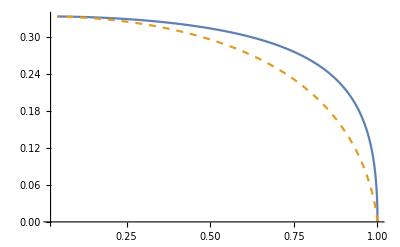

```mathematica
ListLinePlot[{hola,Style[hola2,Dashed]},PlotRange->All]
```

## Definiciones

### Función dieléctrica de tipo Drude

Definiendo la sección transversal de absorción

```mathematica
Cabs[a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,αx,αz,Cabs,Cabsx,Cabsz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Cabs=k Im[2 αx+αz]/3;
										Cabsx=k Im[αx];
										Cabsz=k Im[αz];
										{Cabs,Cabsx,Cabsz}]
```

```mathematica
Csca[a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,αx,αz,Csca,Cscax,Cscaz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Csca=k^4 Norm[2 αx+αz]^2/(18 Pi);
										Cscax=k^4 Norm[αx]^2/(6 Pi);
										Cscaz=k^4 Norm[αz]^2/(6 Pi);
										{Csca,Cscax,Cscaz}]
```

```mathematica
Cext[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[1]]+Cabs[a,b,c,nm,λ,λp,γ][[1]]
Cextx[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[2]]+Cabs[a,b,c,nm,λ,λp,γ][[2]]
Cextz[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[3]]+Cabs[a,b,c,nm,λ,λp,γ][[3]]
```

### Datos experimentales

```mathematica
Cabsexp[a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,αx,αz,Cabs,Cabsx,Cabsz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Cabs=k Im[2αx+ αz]/3;
										Cabsx=k Im[αx];
										Cabsz=k Im[αz];
										{Cabs,Cabsx,Cabsz}]
```

```mathematica
Cscaexp[a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,αx,αz,Csca,Cscax,Cscaz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Csca=k^4 (Norm[αz]^2+Norm[αx]^2+Norm[αx]^2)/(18 Pi);
										Cscax=k^4 Norm[αx]^2/(6 Pi);
										Cscaz=k^4 Norm[αz]^2/(6Pi);
										{Csca,Cscax,Cscaz}]
```

```mathematica
Cextexp[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[1]]+Cabsexp[a,b,c,nm,λ,np][[1]]
Cextexpx[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[2]]+Cabsexp[a,b,c,nm,λ,np][[2]]
Cextexpz[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[3]]+Cabsexp[a,b,c,nm,λ,np][[3]]
```

```mathematica
Cextexp[30,10,10,1.33,144,1]
```

66.7352

## Cálculos

### Datos experimentales

#### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]]*1000;
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
aluminio=Transpose[{λalum,naluminio}];
```

```mathematica
nindexalum=Interpolation[aluminio]
```

InterpolatingFunction[…]

```mathematica
h vlight/300
```

4.13567

Se graficará la Cext promedio contrastada con las Cext individuales

```mathematica
qextAlDrpromedio=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.07}];
qextAlDrx=Table[{h vlight/λ,Cextx[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.07}];
qextAlDrz=Table[{h vlight/λ,Cextz[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.07}];
qextAlSphe=Table[{h vlight/λ,Cextz[1.5,1.5,1.5,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.07}];
```

```mathematica
h vlight/6
```

206.783

```mathematica
upperTicksCext=Module[{labels,positions},labels={138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];

upperTicksMinorCext=Module[{labels,positions,size},labels={3.5,4.2,4.6,6,8,9,12,40};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

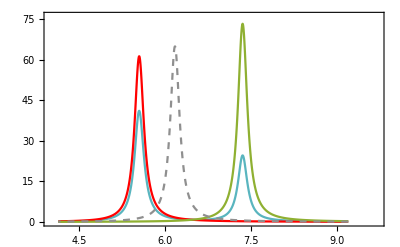

```mathematica
cextAl=ListLinePlot[{Style[qextAlDrpromedio,RGBColor[0.349,0.71,0.749]],Style[qextAlDrx,Red],Style[qextAlDrz,RGBColor[0.560181,0.691569,0.194885]],Style[qextAlSphe,Dashed,RGBColor[0.561,0.561,0.561]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega \:[\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorCext,upperTicksCext]}},PlotRange->{{4,9.7},{0,76}},PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.6]&/@{MaTeX["\langle C_{ext}"],MaTeX["C_{ext}^{(1)}"],MaTeX["C_{ext}^{(3)}"],MaTeX["\langle C_{ext}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.75,0.6}]]
```

```mathematica
Export["CextAlbueno.svg",cextAl]
```

CextAlbueno.svg

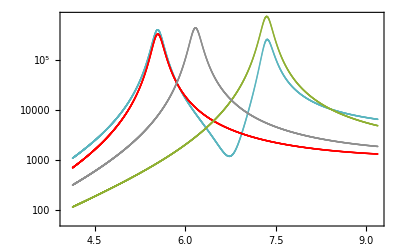

```mathematica
cextAl=ListLogPlot[{Style[qextAlDrpromedio,RGBColor[0.349,0.71,0.749]],Style[qextAlDrx,Red],Style[qextAlDrz,RGBColor[0.560181,0.691569,0.194885]],Style[qextAlSphe,Dashed,RGBColor[0.561,0.561,0.561]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.2],None},{Style[MaTeX["\hbar\omega \:[\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorCext,upperTicksCext]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.2]&/@{MaTeX["\langle C_{ext}"],MaTeX["C_{ext}^{(1)}"],MaTeX["C_{ext}^{(3)}"],MaTeX["\langle C_{ext}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.87,0.73}]]
```

```mathematica
Export["CextAlbueno.svg",cextAl]
```

CextAlbueno.svg

#### Elipsoide oblato

#### Cambiando el tamaño de a

```mathematica
qextAlDr=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.05}];
qextAl1Dr=Table[{h vlight/λ,Cext[1.75,1.75,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.05}];
qextAl2Dr=Table[{h vlight/λ,Cext[2.0,2.0,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
qextAl3Dr=Table[{h vlight/λ,Cext[2.25,2.25,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
qextEsferaDr=Table[{h vlight/λ,Cext[2.0,2.0,2.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
```

```mathematica
upperTicksAl=Module[{labels,positions},labels={124,138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAl=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

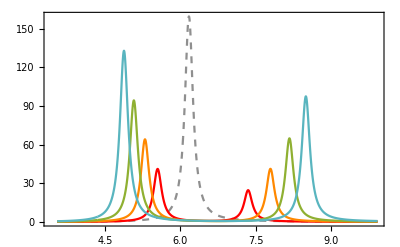

```mathematica
alc=ListLinePlot[{Style[qextEsferaDr,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAlDr,Red],Style[qextAl1Dr,RGBColor[1,0.533,0]],Style[qextAl2Dr,RGBColor[0.560181,0.691569,0.194885]],Style[qextAl3Dr,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorAl,upperTicksAl]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.5]&/@{MaTeX["1"],MaTeX["1.5"],MaTeX["1.75"],MaTeX["2"],MaTeX["2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",3},LegendLabel->Style[MaTeX["\mbox{AR}"],Magnification->1.5]],{0.73,0.75}]]
```

```mathematica
Export["Alc.svg",alc]
```

Alc.svg

#### Misma razón de aspecto

```mathematica
qextAlAR=Table[{h vlight/λ,Cext[1.0,1.0,0.5,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,400,0.01}];
qextAl1AR=Table[{h vlight/λ,Cext[1.5,1.5,0.75,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,400,0.01}];
qextAl2AR=Table[{h vlight/λ,Cext[2.0,2.0,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,400,0.01}];
qextAl3AR=Table[{h vlight/λ,Cext[2.5,2.5,1.25,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,400,0.01}];
qextAl3sphere=Table[{h vlight/λ,Cext[2.0,2.0,2.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,400,0.01}];
```

```mathematica
h vlight/3
```

413.567

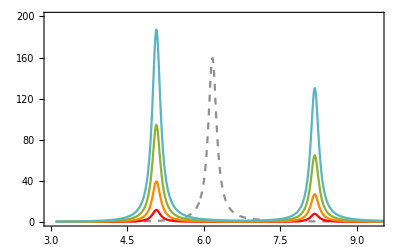

```mathematica
alAR=ListLinePlot[{Style[qextAl3sphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAlAR,Red],Style[qextAl1AR,RGBColor[1,0.533,0]],Style[qextAl2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextAl3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorAl,upperTicksAl]}},PlotRange->{{3,9.4},{0,200}},PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.5]&/@{MaTeX["2\mbox{ nm}"],MaTeX["1\mbox{ nm} "],MaTeX["1.5\mbox{ nm}"],MaTeX["2\mbox{ nm}"],MaTeX["2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},Spacings->{0.03},LegendLayout->{"Column",1},LegendLabel->Style[MaTeX["a"],Magnification->1.5]],{0.15,0.55}]]
```

```mathematica
Export["AlAR.svg",alAR]
```

AlAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qscaAlcontx=Table[{h vlight/λ,Csca[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[2]]},{λ,135,300,0.05}];
qscaAlcontz=Table[{h vlight/λ,Csca[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[3]]},{λ,135,300,0.05}];
qabsAlSphx=Table[{h vlight/λ,Cabs[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[2]]},{λ,135,300,0.05}];
qabsAlSphz=Table[{h vlight/λ,Cabs[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[3]]},{λ,135,300,0.05}];
```

```mathematica
qscaAlcont=Table[{h vlight/λ,Csca[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
qabsAlSph=Table[{h vlight/λ,Cabs[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
```

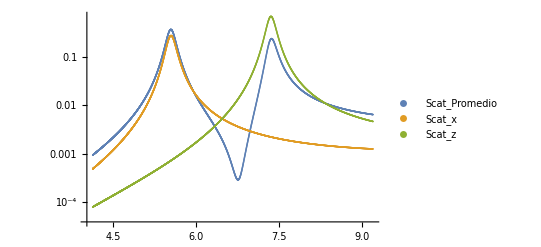

```mathematica
ListLogPlot[{qscaAlcont,qscaAlcontx,qscaAlcontz },PlotRange->All,PlotLegends->{"Scat_Promedio","Scat_x","Scat_z"}]
```

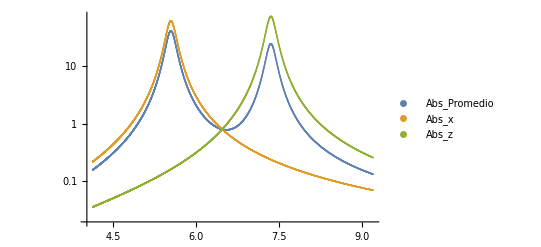

```mathematica
ListLogPlot[{qabsAlSph,qabsAlSphx,qabsAlSphz },PlotRange->All,PlotLegends->{"Abs_Promedio","Abs_x","Abs_z"}]
```

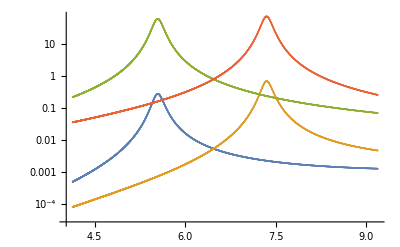

```mathematica
ListLogPlot[{qscaAlcontx,qscaAlcontz,qabsAlSphx,qabsAlSphz},PlotRange->All]
```

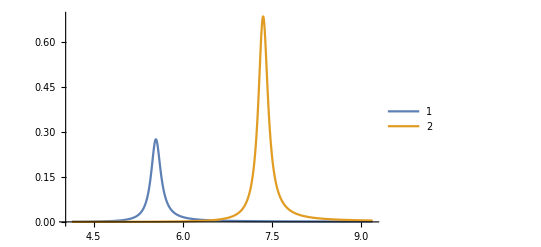

```mathematica
ListLinePlot[{qscaAlcontx,qscaAlcontz},PlotRange->All,PlotLegends->Automatic]
```

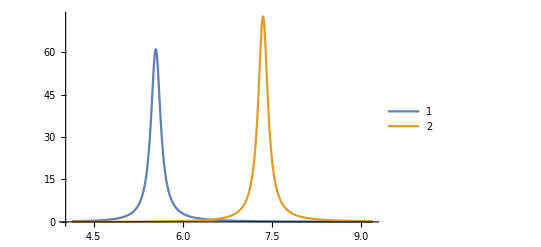

```mathematica
ListLinePlot[{qabsAlSphx,qabsAlSphz},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
qabsAlcont=Table[{h vlight/λ,Cabs[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
qscaAlcont=Table[{h vlight/λ,Csca[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
qextAlcont=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.05}];
qabsAlSph=Table[{h vlight/λ,Cabs[1.5,1.5,1.5,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
qscaAlSph=Table[{h vlight/λ,Csca[1.5,1.5,1.5,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.05}];
```

```mathematica
h vlight/9
```

137.856

```mathematica
upperTicksAl=Module[{labels,positions},labels={138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAl=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

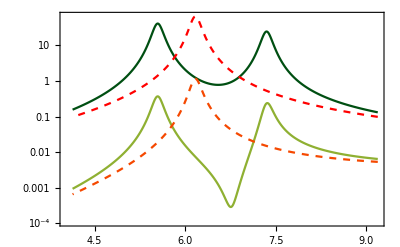

```mathematica
alcont=ListLogPlot[{Style[qabsAlcont,RGBColor[0,0.31,0.071]],Style[qscaAlcont,RGBColor[0.560181,0.691569,0.194885]],Style[qabsAlSph,Dashed,Red],Style[qscaAlSph,Dashed,RGBColor[0.961,0.282,0]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["[\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAl,upperTicksAl]}},PlotRange->All,Joined->True,PlotRange->{{},{130,300}},PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.5]&/@{MaTeX["C_{abs}"],MaTeX["C_{sca}"],MaTeX["C_{abs}"],MaTeX["C_{sca}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",2}],{0.73,0.15}]]
```

```mathematica
Export["AlContribuciones3.svg",alcont]
```

AlContribuciones3.svg

### Oro

Datos obtenidos de Johnson & Christy  DOI: https://doi.org/10.1103/PhysRevB.6.4370

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
au=Import["C:\\Users\\Lunita\\OneDrive\\Documentos\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau11=Drop[Drop[au,{51,101}],1];
kau11=Drop[au,{1,52}];
λAu1=nau11[[All,1]]*1000; (*λ en nm*)
nau1=nau11[[All,2]];
kAu1=kau11[[All,2]];
nAu1=nau1+ I kAu1;
aU1=Transpose[{λAu1,nAu1}];
```

```mathematica
nindexau1=Interpolation[aU1];
```

```mathematica
300/(2*Pi*1.33)
```

35.8996

#### Elipsoide oblato

#### Cambiando el tamaño de a

```mathematica
qextAu1c=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu2c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu3c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu4c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAuEsferac=Table[{h vlight/λ,Cextexp[2,2,2.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qscaAu4c=Table[{h vlight/λ,Cscaexp[2.25,2.25,1.0,1.33,λ,nindexau1[λ]][[1]]},{λ,195,1937}];
qabsAu4c=Table[{h vlight/λ,Cabsexp[2.25,2.25,1.0,1.33,λ,nindexau1[λ]][[1]]},{λ,195,1937}];
```

```mathematica
h vlight/6
```

206.783

```mathematica
upperTicks4=Module[{labels,positions},labels={207,248,310,414,620,1240};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

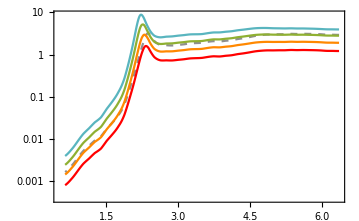

```mathematica
au1c=ListLogPlot[{Style[qextAuEsferac,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAu1c,Red],Style[qextAu2c,RGBColor[1,0.533,0]],Style[qextAu3c,RGBColor[0.560181,0.691569,0.194885]],Style[qextAu4c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["C_{ext} \:[\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,Joined->True,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.5]&/@{MaTeX["1"],MaTeX["1.5"],MaTeX["1.75"],MaTeX["2"],MaTeX["2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",2},LegendLabel->Style[MaTeX["\mbox{AR}"],Magnification->1.5]],{0.75,0.35}]]
```

```mathematica
Export["Auc.svg",au1c]
```

Auc.svg

```mathematica
N[Log10[10]]
```

1.

#### Misma razón de aspecto

```mathematica
qextAuAR=Table[{h vlight/λ,Cextexp[1.0,1.0,0.5,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,.75,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAu3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
qextAuEsferaAR=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexau1[λ]]},{λ,195,1937}];
```

```mathematica
h c/2
```

1.2407×10^-15

```mathematica
upperTicks4=Module[{labels,positions},labels={207,248,310,414,620,1240};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

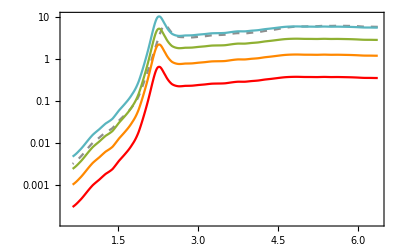

```mathematica
au1AR=ListLogPlot[{Style[qextAuEsferaAR,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAuAR,Red],Style[qextAu1AR,RGBColor[1,0.533,0]],Style[qextAu2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextAu3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,Joined->True,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.5]&/@{MaTeX["2\mbox{ nm}"],MaTeX["1\mbox{ nm} "],MaTeX["1.5\mbox{ nm}"],MaTeX["2\mbox{ nm}"],MaTeX["2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.0,LegendLayout->{"Column",2},LegendLabel->Style[MaTeX["a"],Magnification->1.5]],{0.75,0.35}]]
```

```mathematica
Export["AuAR.svg",au1AR]
```

AuAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsAucont=Table[{λ,Cabsexp[2,2,1,1.33,λ,nindexau1[λ]][[1]]},{λ,300,800}];
qscaAucont=Table[{λ,Cscaexp[2,2,1,1.33,λ,nindexau1[λ]][[1]]},{λ,300,800}];
qextAucont=Table[{λ,Cextexp[2,2,1,1.33,λ,nindexau1[λ]]},{λ,300,800}];
```

```mathematica
h vlight/500
```

2.4814

```mathematica
upperTicks4=Module[{labels,positions},labels={0.8,0.85,0.9,0.95,1,1.1,1.2,1.3,1.4,1.5,1.7,2,2.3,2.5,3.1,4};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={0.8,0.85,0.95,1.15,1.25,1.35,1.45,1.55,1.6,1.65,1.75,1.85,2.1,2.3,2.6,2.8};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

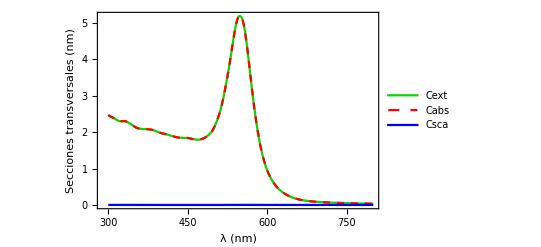

```mathematica
aucont=ListLinePlot[{Style[qextAucont,RGBColor[0.071,0.82,0]],Style[qabsAucont,Red,Dashed],Style[qscaAucont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
(*Export["AuContribuciones1.pdf",aucont]
```

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en nm*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

```mathematica
nindexplata=Interpolation[plata];
```

```mathematica
Table[]
```

#### Oblato

```mathematica
qextAgc=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAg1c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAg2c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAg3c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAgEsferac=Table[{h vlight/λ,Cextexp[2.0,2.0,2.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
```

```mathematica
qabsAg3c=Table[{h vlight/λ,Cabsexp[2.25,2.25,1.0,1.33,λ,nindexplata[λ]][[1]]},{λ,300,550,0.01}];
qscaAg3c=Table[{h vlight/λ,Cscaexp[2.25,2.25,1.0,1.33,λ,nindexplata[λ]][[1]]},{λ,300,550,0.01}];
```

```mathematica
h vlight/3.241372910102672
```

382.77

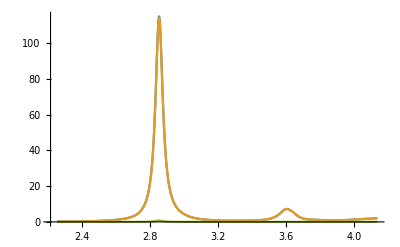

```mathematica
ListLinePlot[{qextAg3c,qabsAg3c,qscaAg3c},PlotRange->All]
```

```mathematica
h vlight/2.5
```

496.28

```mathematica
upperTicksAg=Module[{labels,positions},labels={310,355,414,496};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAg=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

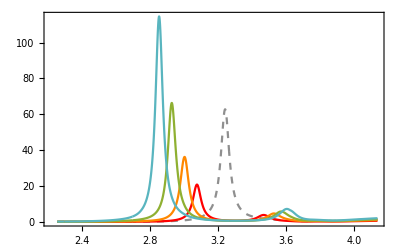

```mathematica
plata1c=ListLinePlot[{Style[qextAgEsferac,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAgc,Red],Style[qextAg1c,RGBColor[1,0.533,0]],Style[qextAg2c,RGBColor[0.560181,0.691569,0.194885]],Style[qextAg3c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega \:[\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.5]&/@{MaTeX["1"],MaTeX["1.5"],MaTeX["1.75"],MaTeX["2"],MaTeX["2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLabel->Style[MaTeX["\mbox{AR}"],Magnification->1.5]],{0.85,0.5}]]
```

```mathematica
Export["Agc.svg",plata1c]
```

Agc.svg

#### Misma razón de aspecto

```mathematica
qextAgAR=Table[{h vlight/λ,Cextexp[1.0,1.0,0.5,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAg1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,0.75,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAg2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAg3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
qextAg3ARsphere=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexplata[λ]]},{λ,300,550,0.01}];
```

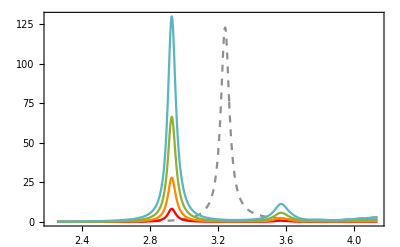

```mathematica
ag1AR=ListLinePlot[{Style[qextAg3ARsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAgAR,Red],Style[qextAg1AR,RGBColor[1,0.533,0]],Style[qextAg2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextAg3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.5]&/@{MaTeX["2.5\mbox{ nm}"],MaTeX["1\mbox{ nm} "],MaTeX["1.5\mbox{ nm}"],MaTeX["2\mbox{ nm}"],MaTeX["2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLabel->Style[MaTeX["a"],Magnification->1.5]],{0.85,0.55}]]
```

```mathematica
Export["AgAR.svg",ag1AR]
```

AgAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsAgcont=Table[{λ,Cabsexp[15,15,1,1.33,λ,nindexplata[λ]][[1]]},{λ,750,950}];
qscaAgcont=Table[{λ,Cscaexp[15,15,1,1.33,λ,nindexplata[λ]][[1]]},{λ,750,950}];
qextAgcont=Table[{λ,Cextexp[15,15,1,1.33,λ,nindexplata[λ]]},{λ,750,950}];
```

```mathematica
h vlight/950
```

1.306

```mathematica
upperTicksAg=Module[{labels,positions},labels={1.3,1.34,1.37,1.4,1.45,1.5,1.55,1.6,1.65};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAg=Module[{labels,positions,size},labels={1.31,1.32,1.33,1.35,1.38,1.43,1.48,1.5,1.53,1.63};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

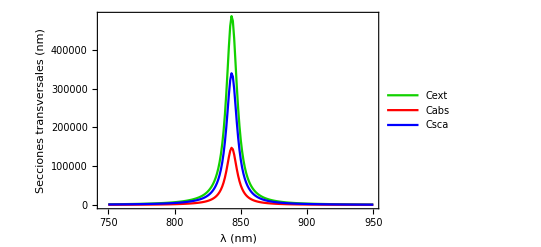

```mathematica
agcont=ListLinePlot[{Style[qextAgcont,RGBColor[0.071,0.82,0]],Style[qabsAgcont,Red],Style[qscaAgcont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
(*Export["AgContribuciones3.pdf",agcont]
```

### Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
bism=Import["C:\\Users\\Lunita\\OneDrive\\Documentos\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

Import::nffil: File C:\Users\Lunita\OneDrive\Documentos\GitHub\Servicio-Social\Notebooks Mathematica\Funciones dieléctricas\Bismuto Hagemann.csv not found during Import.

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]]*1000;(*λ en nm*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

```mathematica
nindexbismuto=Interpolation[bismuto];
```

```mathematica
10/(2*Pi*1.33)
```

1.19665

```mathematica
λBism
```

#### Oblato

```mathematica
qextBic=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexbismuto[λ]]},{λ,310,1550}];
qextBi1c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexbismuto[λ]]},{λ,310,1550}];
qextBi2c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexbismuto[λ]]},{λ,310,1550}];
qextBi3c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexbismuto[λ]]},{λ,310,1550}];
qextBiEsferac=Table[{h vlight/λ,Cextexp[2.25,2.25,2.25,1.33,λ,nindexbismuto[λ]]},{λ,310,1550}];
```

```mathematica
h vlight/557
```

2.22747

```mathematica
h vlight/8.44014
```

147.

```mathematica
h vlight/4
```

310.175

```mathematica
h vlight/50
```

24.814

```mathematica
upperTicksBi=Module[{labels,positions},labels={310,413,620,1241};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorBi=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

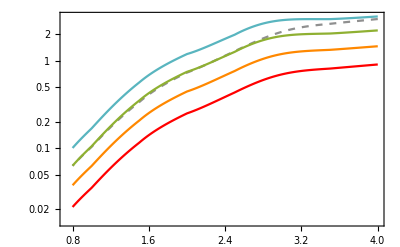

```mathematica
Bismuto1c=ListLogPlot[{Style[qextBiEsferac,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextBic,Red],Style[qextBi1c,RGBColor[1,0.533,0]],Style[qextBi2c,RGBColor[0.560181,0.691569,0.194885]],Style[qextBi3c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorBi,upperTicksBi]}},PlotRange->All,Joined->True,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.5]&/@{MaTeX["1"],MaTeX["1.5"],MaTeX["1.75"],MaTeX["2"],MaTeX["2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",3},LegendLabel->Style[MaTeX["\mbox{AR}"],Magnification->1.5]],{0.75,0.25}]]
```

```mathematica
Export["Bic.svg",Bismuto1c]
```

Bic.svg

```mathematica
h vlight/1500
```

0.827134

```mathematica
4.135667696-0.8271335391999999
```

3.30853

#### Misma razón de aspecto

```mathematica
qextBiAR=Table[{h vlight/λ,Cextexp[1.0,1.0,.5,1.33,λ,nindexbismuto[λ]]},{λ,300,1500}];
qextBi1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,.75,1.33,λ,nindexbismuto[λ]]},{λ,300,1500}];
qextBi2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexbismuto[λ]]},{λ,300,1500}];
qextBi3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexbismuto[λ]]},{λ,300,1500}];
qextBi3ARsphere=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexbismuto[λ]]},{λ,300,1500}];
```

```mathematica
h vlight/120
```

10.3392

```mathematica
1.75/2
```

0.875

```mathematica
Graphics[{Pink,Disk[]},PlotRange->{{-.5,.5},{0,1.5}},PlotRangeClipping->True,Frame->True]
```

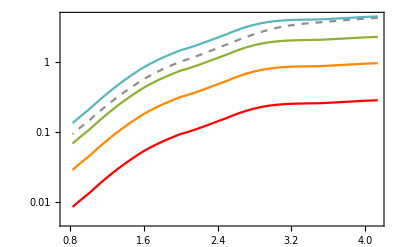

```mathematica
BiAR=ListLogPlot[{Style[qextBi3ARsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextBiAR,Red],Style[qextBi1AR,RGBColor[1,0.533,0]],Style[qextBi2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextBi3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["C_{ext} \:[\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorBi,upperTicksBi]}},PlotRange->All,Joined->True,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.5]&/@{MaTeX["2.5\mbox{ nm}"],MaTeX["1\mbox{ nm} "],MaTeX["1.5\mbox{ nm}"],MaTeX["2\mbox{ nm}"],MaTeX["2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",2},LegendLabel->Style[MaTeX["a"],Magnification->1.5]],{0.75,0.27}]]
```

```mathematica
Export["BisAR.svg",BiAR]
```

BisAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsBicont=Table[{λ,Cabsexp[2,2,0.5,1.33,λ,nindexbismuto[λ]][[1]]},{λ,10,500}];
qscaBicont=Table[{λ,Cscaexp[2,2,0.5,1.33,λ,nindexbismuto[λ]][[1]]},{λ,10,500}];
qextBicont=Table[{λ,Cextexp[2,2,0.5,1.33,λ,nindexbismuto[λ]]},{λ,10,500}];
```

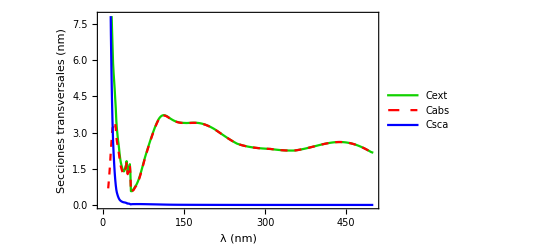

```mathematica
Bismutocont=ListLinePlot[{Style[qextBicont,RGBColor[0.071,0.82,0]],Style[qabsBicont,Red,Dashed],Style[qscaBicont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
(*Export["BiContribuciones1.pdf",Bismutocont]
```

## Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]]*1000 ;(*λ en nm*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

```mathematica
nindexMgO=Interpolation[nmgo];
```

```mathematica
λMgO
```

{360.,410.4,460.8,511.2,561.6,612.,662.4,712.8,763.2,813.6,864.,914.4,964.8,1015.,1066.,1116.,1166.,1217.,1267.,1318.,1368.,1418.,1469.,1519.,1570.,1620.,1670.,1721.,1771.,1822.,1872.,1922.,1973.,2023.,2074.,2124.,2174.,2225.,2275.,2326.,2376.,2426.,2477.,2527.,2578.,2628.,2678.,2729.,2779.,2830.,2880.,2930.,2981.,3031.,3082.,3132.,3182.,3233.,3283.,3334.,3384.,3434.,3485.,3535.,3586.,3636.,3686.,3737.,3787.,3838.,3888.,3938.,3989.,4039.,4090.,4140.,4190.,4241.,4291.,4342.,4392.,4442.,4493.,4543.,4594.,4644.,4694.,4745.,4795.,4846.,4896.,4946.,4997.,5047.,5098.,5148.,5198.,5249.,5299.,5350.,5400.}

#### Oblato

```mathematica
qextMgOc=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexMgO[λ]]},{λ,360,612,0.01}];
qextMgO1c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexMgO[λ]]},{λ,360,612,0.01}];
qextMgO2c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexMgO[λ]]},{λ,360,612,0.01}];
qextMgO3c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexMgO[λ]]},{λ,360,612,0.01}];
qextMgOcsphere=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexMgO[λ]]},{λ,360,612,0.01}];
```

```mathematica
h c/2
```

620.35

```mathematica
upperTicksMgO=Module[{labels,positions},labels={365,388,413,443,477,516,564,620};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorMgO=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

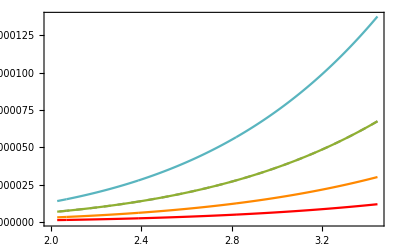

```mathematica
MgO1=ListLinePlot[{Style[qextMgOcsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextMgOc,Red],Style[qextMgO1c,RGBColor[1,0.533,0]],Style[qextMgO2c,RGBColor[0.560181,0.691569,0.194885]],Style[qextMgO3c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorMgO,upperTicksMgO]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.5]&/@{MaTeX["1"],MaTeX["1.5"],MaTeX["1.75"],MaTeX["2"],MaTeX["2.25"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",2},LegendLabel->Style[MaTeX["\mbox{AR}"],Magnification->1.5]],{0.25,0.55}]]
```

```mathematica
Export["MgOc.svg",MgO1]
```

MgOc.svg

```mathematica
qextMgOAR=Table[{h vlight/λ,Cextexp[1.0,1.0,.5,1.33,λ,nindexMgO[λ]]},{λ,360,612,0.01}];
qextMgO1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,.75,1.33,λ,nindexMgO[λ]]},{λ,360,612,0.01}];
qextMgO2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexMgO[λ]]},{λ,360,612,0.01}];
qextMgO3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexMgO[λ]]},{λ,360,612,0.01}];
qextMgO3ARsphere=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexMgO[λ]]},{λ,360,612,0.01}];
```

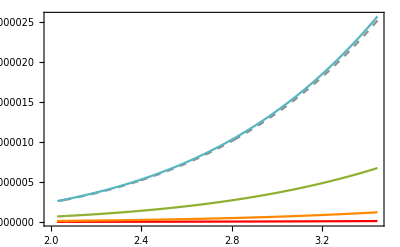

```mathematica
MgO2=ListLinePlot[{Style[qextMgO3ARsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextMgOAR,Red],Style[qextMgO1AR,RGBColor[1,0.533,0]],Style[qextMgO2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextMgO3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],
FrameLabel->{{Style[MaTeX["C_{ext}\: [\mbox{nm}^2]"],Magnification->1.6],None},{Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorMgO,upperTicksMgO]}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[#,Magnification->1.5]&/@{MaTeX["2.5\mbox{ nm}"],MaTeX["1\mbox{ nm} "],MaTeX["1.5\mbox{ nm}"],MaTeX["2\mbox{ nm}"],MaTeX["2.5\mbox{ nm}"]}},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05,LegendLayout->{"Column",2},LegendLabel->Style[MaTeX["a"],Magnification->1.5]],{0.3,0.57}]]
```

```mathematica
Export["MgOAR.svg",MgO2]
```

MgOAR.svg

## Eritrocitos

```mathematica
RBCreal=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\NRealRBC.csv"];
RBCimag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\NImagRBC.csv"];
```

```mathematica
λRBC=RBCreal[[All,1]];
nRBC=RBCreal[[All,2]];
kRBC=RBCimag[[All,2]];
nindRBC=nRBC+ I kRBC;
RBC=Transpose[{λRBC,nindRBC}];
```

```mathematica
nindexRBC=Interpolation[RBC];
```

```mathematica
qabsRBC=Table[{λ,Cabsexp[20,20,12,1.33,λ,nindexRBC[λ]][[1]]},{λ,400,600}];
qscaRBC=Table[{λ,Cscaexp[20,20,12,1.33,λ,nindexRBC[λ]][[1]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexp[20,20,12,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexpx[6,6,2,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexpz[6,6,2,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
```

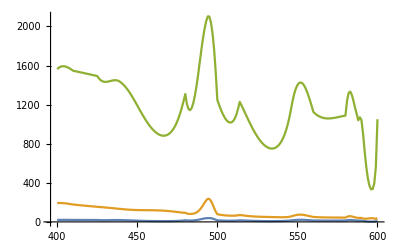

```mathematica
ListLinePlot[{qextRBC,qscaRBC,qabsRBC}]
```

```mathematica
nRBC
```

{1.383,1.365,1.363,1.364,1.365,1.367,1.36481,1.378,1.3728,1.3721,1.361,1.383,1.36053,1.37,1.357,1.3687,1.3668,1.356,1.3667,1.35724,1.356,1.3666}

```mathematica
kRBC
```

{1.4006,1.4007,1.4019,1.404,1.4043,1.4005,1.3993,1.3983,1.3975,1.3973,1.3973,1.3974,1.3974,1.398,1.3978,1.3976,1.3983,1.3975,1.3973,1.39729,1.39728,1.3971}

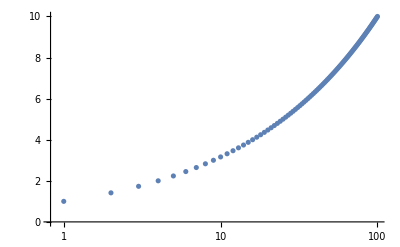

```mathematica
ListLogLinearPlot[Table[{n,Sqrt[n]},{n,100}]]
```

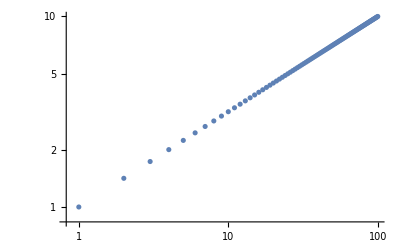

```mathematica
ListLogLogPlot[Table[{n,Sqrt[n]},{n,100}]]
```

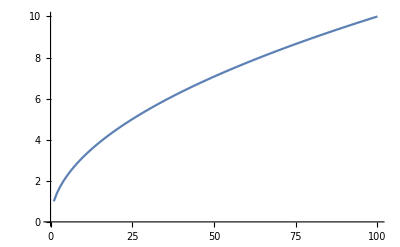

```mathematica
ListLinePlot[Table[{n,Sqrt[n]},{n,100}]]
```